```mathematica
(*
18.821 Project Laboratory in Mathematics
Author: Richard Chen
Created: 09/11/2024 2:39PM
Last Edited: 09/11/2024 2:40PM
*)
```

## Compute Chromatic Polynomials

```mathematica
completeBipartite[n_]:=Return[Graph[Range[2*n], Flatten[Outer[UndirectedEdge, Range[n],Range[n+1,2*n]]]]]
```

```mathematica
rootsChromatic[n_]:=Solve[ChromaticPolynomial[completeBipartite[n],q]==0,q]
```

## Plot Chromatic Polynomial Roots

```mathematica
(*With current method, time maxes out around n=10 for bipartite graph*)
```

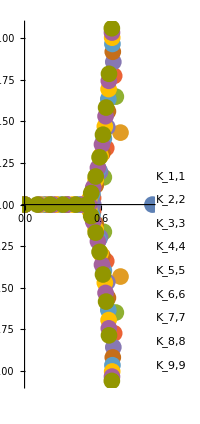

```mathematica
ComplexListPlot[Table[Labeled[Flatten[{q/n}/.rootsChromatic[n]],StringJoin[{"K_",ToString[n],",",ToString[n]}]],{n,1,10}],PlotStyle->PointSize[0.03]]
```

## Cuspidal curves

```mathematica
f[a_]:=a^1.5
```

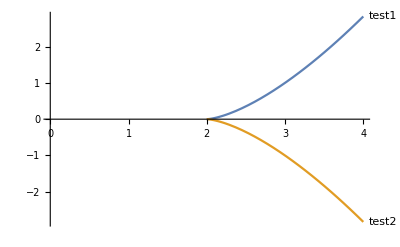

```mathematica
Plot[{Labeled[f[x-2],"test1"],Labeled[-f[x-2],"test2"]},{x,0,4}]
```

## Scratch Cells